```mathematica
y[n_]:=If[FractionalPart[n]==0,UnitStep[n]-UnitStep[n-5],0]
```

```mathematica
x[n_]:=y[n/2]+2y[n/2-1/2]
```

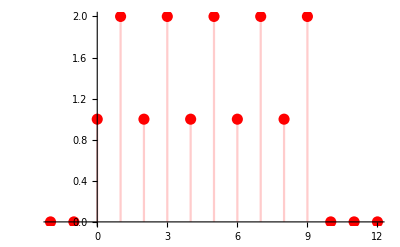

```mathematica
DiscretePlot[{x[n]},{n,-2,12},PlotRange->All,PlotStyle->Directive[PointSize[0.02],Red]]
```